## Massive scalar bound states of a Kerr black hole References: [1] Sam Dolan “Instability of the massive Klein-Gordon field on the Kerr spacetime” (2007) [arXiv:0705.2880]; [2] Emanuele Berti, Vitor Cardoso, Marc Casals, “Eigenvalues and eigenfuntions of spin-weighted spheroidal harmonics in four and higher dimensions” (2006) [arXiv:grqc/0511111] [3] Paolo Pani “Advanced Methods in Black-Hole Perturbation theory” (2013) [arXiv:1305.6759] [4] Review: Richard Brito, Vitor Cardoso and Paolo Pani, “Superradiance: new frontiers in Black Hole Physics” (2020) [arXiv:1501.06570] Written by Richard Brito for the Kavli-Villum Summer School on Gravitational Waves in Corfu, Greece 25-30 Sep 2023, adapted from notebook @https://centra.tecnico.ulisboa.pt/network/grit/files/ringdown/

## Continued-fraction method

This section computes the eigenfrequencies of the quasi-bound states using the continued-fraction method presented in Ref.[1], see their Sec. III. The angular eigenvalues are computed using a similar methods, as outlined in Sec.II A of Ref.[2]. This is among the fastest and most accurate methods to compute the eigenfrequencies.

We first define a generic function LEAVER, such that the eigenfrequencies will be the roots of this function

```mathematica
LEAVER[w_,ar_,mu_,l_,m_,NITMAX_,NITMAX2_]:=(
(*parameters of function LEAVER are: 
w->dimensionlessfrequency Mω, ar->dimensionless spin a/M, mu-> dimensionless constant Mμ, l and m->angular quantum numbers, NITMAX1 and NITMAX2 number of terms in the continued fraction series (they should be sufficiently large for the series to coverge)*)

br=Sqrt[1-ar^2];
rminus=(1-br);
rplus=1+br;
s=0;(*s=0 because we are considering a scalar field. See Ref.[2] for more details*)
k1=1/2*Abs[m-s];
k2=1/2*Abs[m+s];
Alm=l*(l+1)-s*(s+1);
OmegaH=ar/(2*M*rplus);
(**************************************)
(******)
k1=1/2*Abs[m-s];
k2=1/2*Abs[m+s];
wang=√(w^2-mu^2);

γang=Function[n,2*ar*wang*(n+k1+k2+s)];βang=Function[n,n*(n-1)+2*n*(k1+k2+1-2*ar*wang)-(2*ar*wang*(2*k1+s+1)-(k1+k2)*(k1+k2+1))-(ar^2*wang^2+s*(s+1)+Sep)];
αang=Function[n,-2*(n+1)*(n+2*k1+1)];
Leaver31Ang[Sep_]:=Module[{Rn},
For[{n=NITMAX2;Rn=-1.0;},
n>0,
{
Rn=γang[n]/(βang[n]-αang[n]*Rn);n--;}
];Rn];
Leaver33Ang[Sep_]:=βang[0]/αang[0]-Leaver31Ang[Sep];
Alm=FindRoot[Leaver33Ang[Sep]==0,{Sep,Alm}][[1]][[2]];(*Alm is the angular eigenvalue as defined in Ref.[2]*)
(**************************************)
q=-Sqrt[mu^2-w^2];c0=1-2*I*w-2*I/br*(w-ar*m/2);c1=-4+4*I*(w-I*q*(1+br))+4*I/br*(w-ar*m/2)-2*(w^2+q^2)/q;c2=3-2*I*w-2*I/br*(w-ar*m/2)-2*(q^2-w^2)/q;c3=2*I*(w-I*q)^3/q+2*(w-I*q)^2*br+q^2*ar^2+2*I*q*ar*m-Alm-1-(w-I*q)^2/q+2*q*br+2*I/br*((w-I*q)^2/q+1)*(w-ar*m/2);c4=(w-I*q)^4/q^2+2*I*w*(w-I*q)^2/q-2*I/br*(w-I*q)^2/q*(w-ar*m/2);γ=Function[n,n^2+(c2-3)*n+c4+(-c2+2)*0];
β=Function[n,-2*n^2+(c1+2)*n+c3];α=Function[n,n^2+(c0+1)*n+c0];
Leaver31=Module[{Rn},For[{n=NITMAX;Rn=-1.0;},n>0,{Rn=γ[n]/(β[n]-α[n]*Rn);n--;}
];Rn];
Leaver33=β[0]/α[0]-Leaver31 (*by finding roots of this equations we can find eigenfrequencies*));
```

```mathematica
(*seeting a/M=0.9, Mμ=0.2, l=m=1*)
fun[x_?NumberQ]:=LEAVER[x,0.9,0.2,1,1,300,300];
FindRoot[fun[x],{x,0.199+10^-8 I}](*obtain the eigenfrequency Mω. Other modes can  be obtained by using Mω~Mμ(1-(Mμ)^2/(2(n0+l+1))) as a guess with n0 the overtone number (note that the principal quantum number is n=n0+l+1)*)
```

{x→0.198959+1.55615×10^-9 ⅈ}

```mathematica
(*checking that angular eigenvalue I computed is the same as the one given by Mathematica built-in function. Note that Mathematica defines the angular eigenvalue slightly differently from Ref.[2], i.e. Alm=SpheroidalEigenvalue[l,m,a √(μ^2-ω^2)]-a^2(ω^2-μ^2).*)
Alm
SpheroidalEigenvalue[l,m,a √(μ^2-ω^2)]-a^2(ω^2-μ^2)/.l->1/.m->1/.a->0.9/.μ->0.2/.ω->0.19895873376271025+1.5561537936291536*^-9 I
```

2.00007-1.00312×10^-10 ⅈ

2.00007-1.00312×10^-10 ⅈ

## Direct integration method

This section computes the eigenfrequencies of the quasi-bound states using a direct integration method.  This method is discussed for example in Sec. 2.2 of Ref.[3], which we refer to for details

```mathematica
Quit[]
```

### Radial wave equation

```mathematica
(*first I define some useful quantities and the radial equation*)
rplus=M+√(M^2-a^2);
rminus=M-√(M^2-a^2);
rs[r_]:=r+M Log[(r-rplus)(r-rminus)]+(2 M^2)/(2 √(M^2-a^2)) Log[(r-rplus)/(r-rminus)];
Ωh=a/(2M rplus);
F[r_]:=Δ[r]/(r^2+a^2);
Δ[r_]:=r^2-2M r+a^2
V=(Δ[r] μ^2)/(r^2+a^2)+(4M r a m ω-a^2 m^2+Δ[r](Alm+(ω^2-μ^2)a^2))/((r^2+a^2)^2)+(Δ[r](3 r^2-4M r+a^2))/((r^2+a^2)^3)-(3 Δ[r]^2 r^2)/((r^2+a^2)^4);
eqn=F[r]^2 Y''[r]+F'[r]F[r]Y'[r]+(ω^2-V)Y[r]//Simplify;
```

```mathematica
(*rs[r] is the torsoise coordinate defined as (dr_*)/dr=(r^2+a^2)/Δ*)
D[rs[r],r]//Simplify
```

(a^2+r^2)/(a^2-2 M r+r^2)

#### Check asymptotic solutions when r->r_+ and r->∞ (no need to run, this is just to check asymptotic solutions)

Let us find solutions of eqn when r->rp, assuming Y~h0*E^(i k rs) with h0 a constant

```mathematica
Y[r_]:=Exp[I k rs[r]]h0;
eqS=Simplify[eqn/ⅇ^(ⅈ k rs[r])/.rs'[r]->1/F[r]/.D[rs'[r]->1/F[r],r]];
Clear[Y];
```

```mathematica
eqHorizon=(Assuming[{M>a,ω>0},Series[eqS,{r,rplus,0}]//Simplify]//Normal)/.k^2->k2
```

-(h0 (16 a m M^3 (M+√(-a^2+M^2)) ω-4 a^3 m M (3 M+√(-a^2+M^2)) ω+32 M^5 (M+√(-a^2+M^2)) (k2-ω^2)+a^4 (m^2+4 M^2 (k2-ω^2))-2 a^2 (m^2 M (M+√(-a^2+M^2))+8 M^3 (2 M+√(-a^2+M^2)) (k2-ω^2))))/(4 M^2 (M+√(-a^2+M^2))^4)

```mathematica
(*for Y[r]~Exp[I k rs[r]]h0 to be solution when r->r+ we need k^2 to satisfy*)
Solve[eqHorizon==0,k2]//FullSimplify
```

{{k2→(2 m^2 M (M-√(-a^2+M^2))+4 a m M (-M+√(-a^2+M^2)) ω-a^2 (m^2-4 M^2 ω^2))/(4 a^2 M^2)}}

```mathematica
(*check that this is equal to k^2=(ω-m ΩH)^2*)
```

```mathematica
(2 m^2 M (M-√(-a^2+M^2))+4 a m M (-M+√(-a^2+M^2)) ω-a^2 (m^2-4 M^2 ω^2))/(4 a^2 M^2)==(ω-m Ωh)^2//Simplify
```

True

```mathematica
(*ingoing waves at the horizon correspond to chosing k=-(ω-m Ωh). A way to see this is to transform to Kerr-ingoing coordinates (see discussion in Sec. V of https://articles.adsabs.harvard.edu/pdf/1973ApJ...185..635T) and compute group velocity: Subscript[v, g]=dω/dk=-1<0, i.e. wave is propagating towards negative values of r_*.*)
```

Let us find now find solutions when r->inf, assuming Y~hinf*r^ν*E^(- kinf rs) takes the form: h[r]~hinf*r^ν (see eq. 31 in Re[1])

```mathematica
kinf
```

```mathematica
Y[r_]:=Exp[-kinf rs[r]] r^ν hinf;
eqS=Simplify[eqn/(Exp[-kinf rs[r]] r^ν)/.rs'[r]->1/F[r]/.D[rs'[r]->1/F[r],r]];
Clear[Y];
```

```mathematica
eqinf=Assuming[{M>Q,ω>0},Series[eqS,{r,Infinity,1}]//FullSimplify]//Normal
```

(2 hinf (M μ^2-kinf ν))/r+hinf (kinf^2-μ^2+ω^2)

```mathematica
(*for Y~hinf*r^ν*E^(i k rs) to be a solution we therefore need kinf^2=μ^2-ω^2 from the term of order 1/r^0 to vanish, whereas the term of order 1/r requires:*)
```

```mathematica
Solve[(2 hinf (M μ^2-kinf ν))/r==0,ν]
```

{{ν→(M μ^2)/kinf}}

```mathematica
(*this agrees with e.g. eq. 12 in https://arxiv.org/pdf/1901.05592.pdf*)
```

#### Series Horizon

Here we do the standard series expansion at the horizon (see Ref.[2] for details, see also eq. 15 https://arxiv.org/pdf/1901.05592.pdf, which is what we are computing here). The order of the expansion, ORDH, can be set freely. The higher ORDH the more accurate is the computation, but it can be extremely slow to compute all terms in the series expansion for very high ORDH

```mathematica
Y[r_]:=ⅇ^(-ⅈ (ω-m Ωh) rs[r])h[r];
eqS=Simplify[eqn/ⅇ^(-ⅈ (ω-m Ωh) rs[r])/.rs'[r]->1/F[r]/.D[rs'[r]->1/F[r],r]];
Clear[Y];
```

```mathematica
ORDH=3;
h[r_]:=Sum[hh[i] (r-rplus)^i,{i,0,ORDH}]; 
ss=Series[eqS,{r,rplus,ORDH}]//Simplify;
eqsH=Table[SeriesCoefficient[ss,i]==0,{i,1,ORDH}];
yh=Table[hh[i],{i,1,ORDH}];
Length[eqsH]
Length[yh]
seriesH=Solve[eqsH,yh][[1]]//Simplify;
Clear[h]
```

3

3

#### Series Infinity

Here we do the standard series expansion at infinity. Again the order is arbitrary, but the higher the order, the better.

```mathematica
Y[r_]:=ⅇ^(-kk rs[r])r^ν h[r];
eqSinf=Simplify[eqn/(ⅇ^(-kk rs[r])r^ν)/.rs'[r]->1/F[r]/.D[rs'[r]->1/F[r],r]];
Clear[Y];
```

```mathematica
ORDINF=5;
h[r_]:=Sum[hhinf[i] r^-i,{i,0,ORDINF}];
ruleINF={kk^2->μ^2-ω^2,kk^4->(μ^2-ω^2)^2,kk^6->(μ^2-ω^2)^3,ν->(M μ^2)/kk};
ss1=Series[{eqSinf}//.ruleINF,{r,∞,ORDINF}];

eqs1=Table[SeriesCoefficient[ss1[[1]],i]==0,{i,0,ORDINF}];
yinf=Table[hhinf[i],{i,1,ORDINF-1}];
systINF=Solve[eqs1,yinf][[1]]//Simplify;
Clear[h,R]
```

This is needed to extract the coefficients of the asymptotic expansion at infinity with enough precision.

```mathematica
Qinf=((ⅇ^(-kk rs[r])r^ν Sum[hhinf[i]/r^i,{i,0,ORDINF-1}])//.Union[systINF,{hhinf[0]->BB,ν->(M μ^2)/kk,kk-> √(μ^2-ω^2)}])+ ((ⅇ^(-kk rs[r])r^ν Sum[hhinf[i]/r^i,{i,0,ORDINF-1}])//.Union[systINF,{hhinf[0]->CC,ν->(M μ^2)/kk,kk->-√(μ^2-ω^2)}]);
Qpinf=D[Qinf,r];

solBC=Solve[{(Qinf/.r->rinf)==Y1,(Qpinf/.r->rinf)==Y1p},{BB,CC}][[1]];
```

```mathematica
We can store the equations to save time in future (to avoid having to run this part every time) :
```

```mathematica
SetDirectory[NotebookDirectory[]];
Put[{systINF,ORDINF,seriesH,ORDH,eqn,solBC},"series.m"]
```

### Angular wave equation

```mathematica
eqnang=1/Sin[θ] D[Sin[θ]D[S[θ],θ],θ]+(a^2(ω^2-μ^2)Cos[θ]^2-m^2/Sin[θ]^2+Alm)S[θ]//Simplify;
```

#### Check asymptotic solutions when θ->0 and θ->π (no need to run, this is just to check asymptotic solutions)

Let us find solutions of eqn when θ->0, assuming S~θ^k there

```mathematica
S[θ_]:=h0*θ^k;
eqS=Simplify[eqnang/θ^k];
Clear[S];
```

```mathematica
eqθ0=Series[eqS,{θ,0,-1}]//Simplify//Normal
```

(h0 (k^2-m^2))/θ^2

```mathematica
Series[SphericalHarmonicY[2,-2,θ,0],{θ,π,2}]
```

1/4 √(15/(2 π)) (θ-π)^2+O[θ-π]^3

```mathematica
(*for S[θ]~θ^k to be a solution when θ->0 we need k^2=m^2 to satisfy. Note that regularity then requires k=m if m>=0,or k=-m if m<0. So k=|m|*)
```

Let us find solutions of eqn when θ->π, assuming S~(θ-π)^k there

```mathematica
S[θ_]:=h0*(θ-π)^k;
eqS=Simplify[eqnang/(θ-π)^k];
```

```mathematica
eqθπ=Series[eqS,{θ,π,0}]//Simplify//Normal
```

(h0 (k^2-m^2))/(-π+θ)^2+h0 (Alm-k/3-m^2/3-a^2 μ^2+a^2 ω^2)

```mathematica
(*for S[θ]~(θ-π)^k to be a solution when θ->π we need k^2=m^2 to satisfy. Note that regularity then requires k=m if m>=0,or k=-m if m<0. So k=|m|*)
```

#### Series @ θ=0

```mathematica
S[θ_]:=θ^Abs[m] S0[θ];
eqn1=eqnang/θ^Abs[m]//Simplify;
Clear[S]
```

```mathematica
ORD=4;
S0[θ_]:=Sum[s0[i] θ^i,{i,0,ORD}]; 
ss=Series[eqn1,{θ,0,ORD}]//Simplify;
eqsH=Table[SeriesCoefficient[ss,i]==0,{i,0,ORD-1}];
yh=Table[s0[i],{i,1,ORD}];
Length[eqsH]
Length[yh]
seriesang0=Solve[eqsH,yh][[1]]//Simplify;
Clear[S0]
```

4

4

```mathematica
seriesang0
```

{s0[1]→0,s0[2]→((3 Alm-m^2-3 a^2 μ^2+3 a^2 ω^2-Abs[m]) s0[0])/(3 (-4+m^2-4 Abs[m]-Abs[m]^2)),s0[3]→0,s0[4]→((-3 m^2+45 a^2 μ^2-45 a^2 ω^2-Abs[m]-(5 (3 Alm-m^2-3 a^2 μ^2+3 a^2 ω^2-Abs[m]) (2-3 Alm+m^2+3 a^2 μ^2-3 a^2 ω^2+Abs[m]))/(-4+m^2-4 Abs[m]-Abs[m]^2)) s0[0])/(45 (-16+m^2-8 Abs[m]-Abs[m]^2))}

#### Series @ θ=π (this is not really needed, since it is identical to the BCs at θ=0, which follows from symmetry considerations, just used as a check)

```mathematica
S[θ_]:=(θ-π)^Abs[m] S0[θ];
eqn1=eqnang/(θ-π)^Abs[m]//Simplify;
Clear[S]
```

```mathematica
ORD=4;
S0[θ_]:=Sum[s0[i] (θ-π)^i,{i,0,ORD}]; 
ss=Series[eqn1,{θ,π,ORD}]//Simplify;
eqsH=Table[SeriesCoefficient[ss,i]==0,{i,0,ORD-1}];
yh=Table[s0[i],{i,1,ORD}];
Length[eqsH]
Length[yh]
seriesangpi=Solve[eqsH,yh][[1]]//Simplify;
Clear[S0]
```

4

4

```mathematica
seriesang0==seriesangpi//Simplify
```

True

```mathematica
SetDirectory[NotebookDirectory[]];
Put[{seriesang0,ORD,eqnang},"seriesang.m"]
```

### Integrator

```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]];
ext=Get["series.m"];
extang=Get["seriesang.m"];

seriesH=ext[[3]];
ORDH=ext[[4]];
eqn=ext[[5]];
solBC=ext[[6]];

seriesang0=extang[[1]];
ORD=extang[[2]];
eqnang=extang[[3]];

rplus=M+√(M^2-a^2);
rminus=M-√(M^2-a^2);
rs[r_]:=r+M Log[(r-rplus)(r-rminus)]+(2 M^2)/(2 √(M^2-a^2)) Log[(r-rplus)/(r-rminus)];
Ωh=a/(2M rplus);
```

```mathematica
(*define a function where ODEs are integrated*)
INT[ω0_,μ0_,a0_,Alm0_,l0_,m0_,EPS_,INF0_]:=(
ruleP={AccuracyGoal->Automatic,PrecisionGoal->Automatic,MaxSteps->Automatic};(*you can play around with these numbers to increase accuracy and precision. Using Mathematica's default (which you can set using "Automatic" is normally faster but less accurate*)

param={ω->ω0,μ->μ0,a->a0,Alm->Alm0,l->l0,m->m0,hh[0]->1,s0[0]->1,kk->√(μ0^2-ω0^2)};
M=1;
rh=M+√(M^2-a^2)//.param;
rhn=rh(1+EPS);(*set numerical horizon at r=r_+(1+ϵ), with ϵ<<1. Normally ϵ~10^-4 is enough for good convergence*)
INF=INF0;(*set numerical infinity at some at some large radius. For bound states I usually use INF~50/(Mμ)^2 of even less. It normally helps to start with smaller INF to get a first guess and then increase INF to get more accurate results*)

(*solve angular equation*)
Sang=θ^Abs[m] Sum[s0[i] θ^i,{i,0,ORD}]//.Union[seriesang0];
BCang={S[EPS]==Sang/.θ->EPS,S'[EPS]==D[Sang,θ]/.θ->EPS}//.param;
EQang={eqnang==0}//.param;
solang=NDSolve[Union[EQang,BCang],S[θ],{θ,EPS,π-EPS},ruleP];
Sn=S[θ]/.solang[[1]];

(*set BCs for S(θ) at θ=π. The term (-1)^(l+m) comes from the symmetry properties of S(θ) under θ->θ-π. This can "guessed" by looking at what properties from the spherical harmonics*)
BCπ=Sn-(-1)^l(θ-π)^Abs[m] Sum[s0[i] (θ-π)^i,{i,0,ORD}]//.Union[seriesang0,param,{θ->π-EPS}];

(*solve radial equation*)
λ=Alm+a^2 ω^2-2a m ω//.param;
Yg=ⅇ^(-ⅈ (ω-m Ωh) rs[r]) Sum[hh[i](r-rh)^i,{i,0,ORDH}]//.Union[param,seriesH];
BCs={Y[rhn]==Yg/.r->rhn,Y'[rhn]==D[Yg,r]/.r->rhn}//.param;
EQs={eqn==0}//.param;
sol=NDSolve[Union[EQs,BCs],Y[r],{r,rhn,INF},ruleP];

Yn=Y[r]/.sol[[1]];
Ynp=D[Yn,r];

(*get coefficients of solutions at infinity*)
CCn=CC//.Union[solBC,param,{rinf->INF,Y1->Yn,Y1p->Ynp,r->INF}];
BBn=BB//.Union[solBC,param,{rinf->INF,Y1->Yn,Y1p->Ynp,r->INF}];

(*we want BCπ and CCn to be zero for BCs to be satisfied*)
{BCπ,CCn});
```

```mathematica
(*check that functions works*)
(*INT[ω0_,μ0_,a0_,Alm0_,l0_,m0_,EPS_,INF0_]*)
INT[0.19895873376271025+1.5561537936291536*^-9 ⅈ,0.2,0.9,2.0007,1,1,10^-3,1000]
```

{-0.421718-6.68018×10^-8 ⅈ,266.701-157.651 ⅈ}

```mathematica
(*root finder*)
μ00=0.2;
l00=1;
m00=1;
a00=0.9;
ωguess=0.19895873376271025+1.5561537936291536*^-9 ⅈ;(*here I'll use the values obtained from the continued fraction method as a guess*)
Aguess=l(l+1)/.l->l00;(*in the limit a=0,Alm=l(l+1) so we can use it as a guess*)
f4[ω_?NumberQ,Alm_?NumberQ]:=INT[ω,μ00,a00,Alm,l00,m00,10^-4,30/μ00^2];
FindRoot[f4[x,y],{{x,ωguess},{y,Aguess}}]
```

{x→0.198959+1.55606×10^-9 ⅈ,y→2.00007-1.00306×10^-10 ⅈ}

```mathematica
(*if you compare with numbers obtained with continued fraction method above, you'll see that numbers are almost the same up to numerical errors*)
```

```mathematica
(*this is just to normalize the angular function as (∫_0)^π sin[θ]|S[θ]|^2=1/(2π)*)
NN=1/(√(NIntegrate[Sn*Conjugate[Sn]Sin[θ],{θ,10^-4,π-10^-4}]2π))
```

0.345485

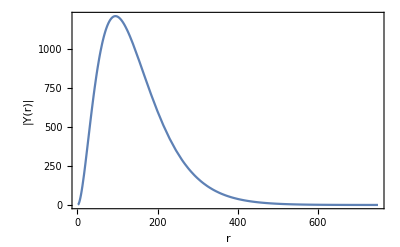

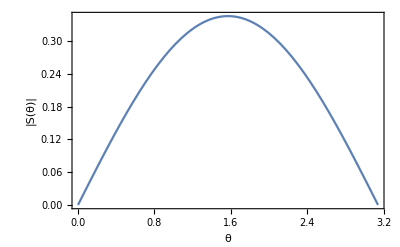

```mathematica
(*check that radial and angular eigenfunctions are indeed regular at the boundaries*)
Plot[{Abs[Yn]},{r,rhn,INF},PlotRange->All,Frame->True,FrameLabel->{"r","|Y(r)|"}]
Plot[{Abs[Sn]*NN},{θ,10^-4,π-10^-4},PlotRange->All,Frame->True,FrameLabel->{"θ","|S(θ)|"}]
```